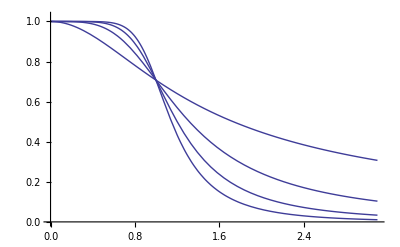

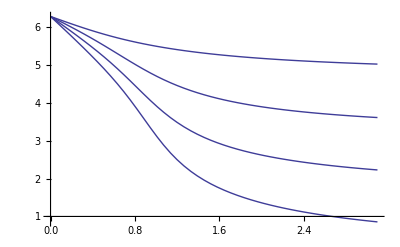

```mathematica
β[k_,m_]:=Exp[I*π/2*(1+(2*k-1)/m)];
λ[m_,f_]:=1/Product[I*f-β[k,m],{k,1,m}];
mod2pi[x_]:=x - Floor[x/2/π]*2*π
Plot[Table[Abs[λ[k,f]],{k,1,4}],{f,0,3.1},PlotRange->{0,1.025}]
Plot[Table[mod2pi[Arg[λ[k,f]]],{k,1,4}],{f,0,3.1},PlotRange->All]
```

```mathematica
β[k,m]==I*Cos[Pi*(2*k-1)/2/m]-Sin[Pi*(2*k-1)/2/m]
```

True